## The Problem

We have a cylindrical photobioreactor of radius R. Let’s take a cross section of this cylinder and look at it from above. For this cross section we can define any point in the reactor with a vector r whose length is rp, the distance measured in centimeters from the center of the cross section, and whose direction is θp, the angle described by r.

For a given vector r, the distance L from the surface of the photobioreactor determines the intensity at the tip of r. For any r and θ, the expression for L is the following:

L(r,θ) = Abs[√(R^2- r Cos^2 θ)- r Sinθ] for r = 0 to R and θ = 0 to 2π

The Beer-Lambert law gives the value of the intensity I for all values of r and θ:

I(r,θ) = I_0 10^(-ϵCL(r,θ)) where I_0= 100 and ϵC = 0.051512

Let’s calculate the values for I for a cylindrical photobioreactor of radius R = 4 cm.

## Calculation of Intensities

Initial conditions and the Beer-Lambert equation.

```mathematica
R = 4;
intensity0 = 100;
ϵC = 0.051512;
L[r_,θ_] := Abs[Sqrt[R^2 - r (Cos[θ])^2]- r Sin[θ]];
Intensity[r_, θ_]:= intensity0 * 10^(-ϵC L[r,θ]);
```

Tests inputs to ensure that outputs make sense.

```mathematica
L[2,π/2]
```

2

```mathematica
L[2, -π/2]
```

6

```mathematica
Intensity[3, #] & /@ {0, π/2, π, 3 π/2, 2 π}
```

{65.2035,88.8153,65.2035,43.5929,65.2035}

```mathematica
α=ϵC Abs[Sqrt[R^2 - x^2]- y];
```

Here the exponential component of the intensity function has been simplified as follows:

x=√r_p*Cos θ_p

y=r_p*Sin θ_p

Notice that (3), the formula used is slightly different from the second term that appears under the square root in equation (1). The difference is that √r_p is used instead of r_(p.)

## Interactive Contour Plot of Intensity

The following allows you to interact with the contour plot by changing the radius r of the photobioreactor.

```mathematica
mcp2 = Manipulate[
α=ϵC Abs[Sqrt[r^2 - x^2]- y];
ContourPlot[intensity0 10^-α, {x, -r, r}, {y, -r,r},
PlotRange->{0,intensity0},
RegionFunction->Function[{x,y},Sqrt[(x^2 + y^2)] ≤ r],
Contours->20,
PlotLabel->"Externally Radiated Surface with " <> ToString[r] <> " cm Radius",
AxesLabel->Automatic , 
ContourLabels->All,
ColorFunction->{"DeepSeaColors"},
Mesh->False,
BoundaryStyle->Automatic, ImageSize-> 500, PlotLegends-> None], 
 {{r, 5, "Radius"},1,10,1,Appearance->"Labeled"}, 
{{intensity0, 50, "Intensity"}, 10,100,10, Appearance-> "Labeled"},
{{ϵC, 0.05, "Concentration"}, 0.01,0.1,0.01, Appearance-> "Labeled"}]
```

## Simulations

```mathematica
beerLambert[intensity_, radius_, concentration_, output_:"contour",{xCoord_:0, yCoord_:0}]:= Module[{alphaC, alphaN, attenIntensityC, attenIntensityN, cPlot, lPlot},
(* intensity is the intensity of light used *)
(* radius is the radius of the cylindrical cross section of the vessel *)
(* concentration is the molar attenuation coefficient multiplied by the number density *)
(* output can be "contour" or "numerical" *)
(* By default, the function draws a contour plot of intensities in the cross section of the vessel *)
(* output = "numerical" gives the intensity at the particular point in the vessel cross section defined by (xCoord,yCoord) *)
(* The numerical output is for use in ListLinePlots *)

(* For the countour plot, keep it it as a parametric equation in x and y *)
If[output == "contour", 
alphaC=concentration * Abs[Sqrt[radius^2 - x^2]- y];
attenIntensityC = intensity * 10^-alphaC;
cPlot =ContourPlot[attenIntensityC, {x, -radius, radius}, {y, -radius, radius},
PlotRange-> All,
RegionFunction->Function[{x,y},Sqrt[(x^2 + y^2)] ≤ radius],
Contours->20,
PlotLabel-> "Radius = " <> ToString[radius] <> " cm, Initial Intensity = " <> ToString[intensity] <> ", Concentration = " <> ToString[concentration],
AxesLabel->Automatic, 
ContourLabels->All,
Frame-> True,
FrameTicks-> {{{-radius, radius,0.5}, None}, {{-radius, radius,0.5}, None}},
ColorFunction->{"DeepSeaColors"},
Mesh->False,
BoundaryStyle->Automatic, 
ImageSize-> Large, 
PlotLegends-> None,
BaseStyle-> {Orange, Bold, 12}, 
LabelStyle -> {Black, 14}];
];

(* For a numerical answer at a particular point (xCoord, yCoord) in the cross section of the vessel, plug in the coordinates *)
If[output == "numerical",
alphaN=concentration * Abs[Sqrt[radius^2 - xCoord^2]- yCoord];
attenIntensityN = intensity * 10^-alphaN;
lPlot = {attenIntensityN, yCoord};
];

Switch[output, "contour", cPlot, "numerical", lPlot, _, lPlot]
];
```

## Numerical Results

### Numerical values: intensity and concentration are fixed while radius varies from 3 to 6 to 9 cm

```mathematica
radiusVarNum = Table[beerLambert[100,i,0.05, "numerical", #] & /@ Table[{0,j}, {j,-i, i, 0.1}], {i, 3,9,3}]
```

{{{50.1187,-3.},{50.6991,-2.9},{51.2861,-2.8},{51.88,-2.7},{52.4807,-2.6},{53.0884,-2.5},{53.7032,-2.4},{54.325,-2.3},{54.9541,-2.2},{55.5904,-2.1},{56.2341,-2.},{56.8853,-1.9},{57.544,-1.8},{58.2103,-1.7},{58.8844,-1.6},{59.5662,-1.5},{60.256,-1.4},{60.9537,-1.3},{61.6595,-1.2},{62.3735,-1.1},{63.0957,-1.},{63.8263,-0.9},{64.5654,-0.8},{65.3131,-0.7},{66.0693,-0.6},{66.8344,-0.5},{67.6083,-0.4},{68.3912,-0.3},{69.1831,-0.2},{69.9842,-0.1},{70.7946,0.},{71.6143,0.1},{72.4436,0.2},{73.2825,0.3},{74.131,0.4},{74.9894,0.5},{75.8578,0.6},{76.7361,0.7},{77.6247,0.8},{78.5236,0.9},{79.4328,1.},{80.3526,1.1},{81.2831,1.2},{82.2243,1.3},{83.1764,1.4},{84.1395,1.5},{85.1138,1.6},{86.0994,1.7},{87.0964,1.8},{88.1049,1.9},{89.1251,2.},{90.1571,2.1},{91.2011,2.2},{92.2571,2.3},{93.3254,2.4},{94.4061,2.5},{95.4993,2.6},{96.6051,2.7},{97.7237,2.8},{98.8553,2.9},{100.,3.}},{{25.1189,-6.},{25.4097,-5.9},{25.704,-5.8},{26.0016,-5.7},{26.3027,-5.6},{26.6073,-5.5},{26.9153,-5.4},{27.227,-5.3},{27.5423,-5.2},{27.8612,-5.1},{28.1838,-5.},{28.5102,-4.9},{28.8403,-4.8},{29.1743,-4.7},{29.5121,-4.6},{29.8538,-4.5},{30.1995,-4.4},{30.5492,-4.3},{30.903,-4.2},{31.2608,-4.1},{31.6228,-4.},{31.989,-3.9},{32.3594,-3.8},{32.7341,-3.7},{33.1131,-3.6},{33.4965,-3.5},{33.8844,-3.4},{34.2768,-3.3},{34.6737,-3.2},{35.0752,-3.1},{35.4813,-3.},{35.8922,-2.9},{36.3078,-2.8},{36.7282,-2.7},{37.1535,-2.6},{37.5837,-2.5},{38.0189,-2.4},{38.4592,-2.3},{38.9045,-2.2},{39.355,-2.1},{39.8107,-2.},{40.2717,-1.9},{40.738,-1.8},{41.2098,-1.7},{41.6869,-1.6},{42.1697,-1.5},{42.658,-1.4},{43.1519,-1.3},{43.6516,-1.2},{44.157,-1.1},{44.6684,-1.},{45.1856,-0.9},{45.7088,-0.8},{46.2381,-0.7},{46.7735,-0.6},{47.3151,-0.5},{47.863,-0.4},{48.4172,-0.3},{48.9779,-0.2},{49.545,-0.1},{50.1187,0.},{50.6991,0.1},{51.2861,0.2},{51.88,0.3},{52.4807,0.4},{53.0884,0.5},{53.7032,0.6},{54.325,0.7},{54.9541,0.8},{55.5904,0.9},{56.2341,1.},{56.8853,1.1},{57.544,1.2},{58.2103,1.3},{58.8844,1.4},{59.5662,1.5},{60.256,1.6},{60.9537,1.7},{61.6595,1.8},{62.3735,1.9},{63.0957,2.},{63.8263,2.1},{64.5654,2.2},{65.3131,2.3},{66.0693,2.4},{66.8344,2.5},{67.6083,2.6},{68.3912,2.7},{69.1831,2.8},{69.9842,2.9},{70.7946,3.},{71.6143,3.1},{72.4436,3.2},{73.2825,3.3},{74.131,3.4},{74.9894,3.5},{75.8578,3.6},{76.7361,3.7},{77.6247,3.8},{78.5236,3.9},{79.4328,4.},{80.3526,4.1},{81.2831,4.2},{82.2243,4.3},{83.1764,4.4},{84.1395,4.5},{85.1138,4.6},{86.0994,4.7},{87.0964,4.8},{88.1049,4.9},{89.1251,5.},{90.1571,5.1},{91.2011,5.2},{92.2571,5.3},{93.3254,5.4},{94.4061,5.5},{95.4993,5.6},{96.6051,5.7},{97.7237,5.8},{98.8553,5.9},{100.,6.}},{{12.5893,-9.},{12.735,-8.9},{12.8825,-8.8},{13.0317,-8.7},{13.1826,-8.6},{13.3352,-8.5},{13.4896,-8.4},{13.6458,-8.3},{13.8038,-8.2},{13.9637,-8.1},{14.1254,-8.},{14.2889,-7.9},{14.4544,-7.8},{14.6218,-7.7},{14.7911,-7.6},{14.9624,-7.5},{15.1356,-7.4},{15.3109,-7.3},{15.4882,-7.2},{15.6675,-7.1},{15.8489,-7.},{16.0325,-6.9},{16.2181,-6.8},{16.4059,-6.7},{16.5959,-6.6},{16.788,-6.5},{16.9824,-6.4},{17.1791,-6.3},{17.378,-6.2},{17.5792,-6.1},{17.7828,-6.},{17.9887,-5.9},{18.197,-5.8},{18.4077,-5.7},{18.6209,-5.6},{18.8365,-5.5},{19.0546,-5.4},{19.2752,-5.3},{19.4984,-5.2},{19.7242,-5.1},{19.9526,-5.},{20.1837,-4.9},{20.4174,-4.8},{20.6538,-4.7},{20.893,-4.6},{21.1349,-4.5},{21.3796,-4.4},{21.6272,-4.3},{21.8776,-4.2},{22.1309,-4.1},{22.3872,-4.},{22.6464,-3.9},{22.9087,-3.8},{23.1739,-3.7},{23.4423,-3.6},{23.7137,-3.5},{23.9883,-3.4},{24.2661,-3.3},{24.5471,-3.2},{24.8313,-3.1},{25.1189,-3.},{25.4097,-2.9},{25.704,-2.8},{26.0016,-2.7},{26.3027,-2.6},{26.6073,-2.5},{26.9153,-2.4},{27.227,-2.3},{27.5423,-2.2},{27.8612,-2.1},{28.1838,-2.},{28.5102,-1.9},{28.8403,-1.8},{29.1743,-1.7},{29.5121,-1.6},{29.8538,-1.5},{30.1995,-1.4},{30.5492,-1.3},{30.903,-1.2},{31.2608,-1.1},{31.6228,-1.},{31.989,-0.9},{32.3594,-0.8},{32.7341,-0.7},{33.1131,-0.6},{33.4965,-0.5},{33.8844,-0.4},{34.2768,-0.3},{34.6737,-0.2},{35.0752,-0.1},{35.4813,0.},{35.8922,0.1},{36.3078,0.2},{36.7282,0.3},{37.1535,0.4},{37.5837,0.5},{38.0189,0.6},{38.4592,0.7},{38.9045,0.8},{39.355,0.9},{39.8107,1.},{40.2717,1.1},{40.738,1.2},{41.2098,1.3},{41.6869,1.4},{42.1697,1.5},{42.658,1.6},{43.1519,1.7},{43.6516,1.8},{44.157,1.9},{44.6684,2.},{45.1856,2.1},{45.7088,2.2},{46.2381,2.3},{46.7735,2.4},{47.3151,2.5},{47.863,2.6},{48.4172,2.7},{48.9779,2.8},{49.545,2.9},{50.1187,3.},{50.6991,3.1},{51.2861,3.2},{51.88,3.3},{52.4807,3.4},{53.0884,3.5},{53.7032,3.6},{54.325,3.7},{54.9541,3.8},{55.5904,3.9},{56.2341,4.},{56.8853,4.1},{57.544,4.2},{58.2103,4.3},{58.8844,4.4},{59.5662,4.5},{60.256,4.6},{60.9537,4.7},{61.6595,4.8},{62.3735,4.9},{63.0957,5.},{63.8263,5.1},{64.5654,5.2},{65.3131,5.3},{66.0693,5.4},{66.8344,5.5},{67.6083,5.6},{68.3912,5.7},{69.1831,5.8},{69.9842,5.9},{70.7946,6.},{71.6143,6.1},{72.4436,6.2},{73.2825,6.3},{74.131,6.4},{74.9894,6.5},{75.8578,6.6},{76.7361,6.7},{77.6247,6.8},{78.5236,6.9},{79.4328,7.},{80.3526,7.1},{81.2831,7.2},{82.2243,7.3},{83.1764,7.4},{84.1395,7.5},{85.1138,7.6},{86.0994,7.7},{87.0964,7.8},{88.1049,7.9},{89.1251,8.},{90.1571,8.1},{91.2011,8.2},{92.2571,8.3},{93.3254,8.4},{94.4061,8.5},{95.4993,8.6},{96.6051,8.7},{97.7237,8.8},{98.8553,8.9},{100.,9.}}}

### Test it out

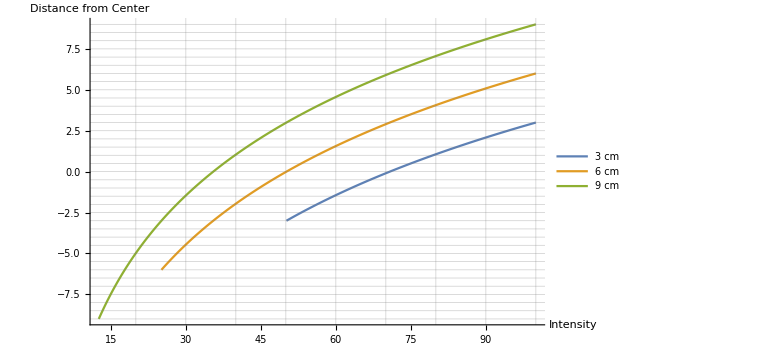

```mathematica
radiusVarLine = ListLinePlot[radiusVarNum, PlotRange-> {{100,0},{-9,9}}, GridLines -> {Range[0,100,10], Range[-9,9,0.5]}, AxesLabel->{"Intensity", "Distance from Center"}, AxesOrigin->{0,0}, LabelStyle-> {Black,Bold, 10}, PlotLegends->{"3 cm", "6 cm", "9 cm"}, ImageSize->Large]
```

### Numerical values: radius and concentration are fixed while intensity varies from 50 to 100 to 150

```mathematica
intensityVarNum = Table[beerLambert[i,6,0.05, "numerical", #] & /@ Table[{0,j}, {j,-6, 6, 0.1}], {i, 50,150,50}]
```

{{{12.5594,-6.},{12.7049,-5.9},{12.852,-5.8},{13.0008,-5.7},{13.1513,-5.6},{13.3036,-5.5},{13.4577,-5.4},{13.6135,-5.3},{13.7711,-5.2},{13.9306,-5.1},{14.0919,-5.},{14.2551,-4.9},{14.4202,-4.8},{14.5871,-4.7},{14.756,-4.6},{14.9269,-4.5},{15.0998,-4.4},{15.2746,-4.3},{15.4515,-4.2},{15.6304,-4.1},{15.8114,-4.},{15.9945,-3.9},{16.1797,-3.8},{16.367,-3.7},{16.5566,-3.6},{16.7483,-3.5},{16.9422,-3.4},{17.1384,-3.3},{17.3368,-3.2},{17.5376,-3.1},{17.7407,-3.},{17.9461,-2.9},{18.1539,-2.8},{18.3641,-2.7},{18.5768,-2.6},{18.7919,-2.5},{19.0095,-2.4},{19.2296,-2.3},{19.4523,-2.2},{19.6775,-2.1},{19.9054,-2.},{20.1359,-1.9},{20.369,-1.8},{20.6049,-1.7},{20.8435,-1.6},{21.0848,-1.5},{21.329,-1.4},{21.576,-1.3},{21.8258,-1.2},{22.0785,-1.1},{22.3342,-1.},{22.5928,-0.9},{22.8544,-0.8},{23.1191,-0.7},{23.3868,-0.6},{23.6576,-0.5},{23.9315,-0.4},{24.2086,-0.3},{24.4889,-0.2},{24.7725,-0.1},{25.0594,0.},{25.3495,0.1},{25.6431,0.2},{25.94,0.3},{26.2404,0.4},{26.5442,0.5},{26.8516,0.6},{27.1625,0.7},{27.477,0.8},{27.7952,0.9},{28.1171,1.},{28.4426,1.1},{28.772,1.2},{29.1052,1.3},{29.4422,1.4},{29.7831,1.5},{30.128,1.6},{30.4768,1.7},{30.8298,1.8},{31.1867,1.9},{31.5479,2.},{31.9132,2.1},{32.2827,2.2},{32.6565,2.3},{33.0347,2.4},{33.4172,2.5},{33.8041,2.6},{34.1956,2.7},{34.5915,2.8},{34.9921,2.9},{35.3973,3.},{35.8072,3.1},{36.2218,3.2},{36.6412,3.3},{37.0655,3.4},{37.4947,3.5},{37.9289,3.6},{38.3681,3.7},{38.8124,3.8},{39.2618,3.9},{39.7164,4.},{40.1763,4.1},{40.6415,4.2},{41.1121,4.3},{41.5882,4.4},{42.0698,4.5},{42.5569,4.6},{43.0497,4.7},{43.5482,4.8},{44.0524,4.9},{44.5625,5.},{45.0786,5.1},{45.6005,5.2},{46.1286,5.3},{46.6627,5.4},{47.203,5.5},{47.7496,5.6},{48.3025,5.7},{48.8619,5.8},{49.4277,5.9},{50.,6.}},{{25.1189,-6.},{25.4097,-5.9},{25.704,-5.8},{26.0016,-5.7},{26.3027,-5.6},{26.6073,-5.5},{26.9153,-5.4},{27.227,-5.3},{27.5423,-5.2},{27.8612,-5.1},{28.1838,-5.},{28.5102,-4.9},{28.8403,-4.8},{29.1743,-4.7},{29.5121,-4.6},{29.8538,-4.5},{30.1995,-4.4},{30.5492,-4.3},{30.903,-4.2},{31.2608,-4.1},{31.6228,-4.},{31.989,-3.9},{32.3594,-3.8},{32.7341,-3.7},{33.1131,-3.6},{33.4965,-3.5},{33.8844,-3.4},{34.2768,-3.3},{34.6737,-3.2},{35.0752,-3.1},{35.4813,-3.},{35.8922,-2.9},{36.3078,-2.8},{36.7282,-2.7},{37.1535,-2.6},{37.5837,-2.5},{38.0189,-2.4},{38.4592,-2.3},{38.9045,-2.2},{39.355,-2.1},{39.8107,-2.},{40.2717,-1.9},{40.738,-1.8},{41.2098,-1.7},{41.6869,-1.6},{42.1697,-1.5},{42.658,-1.4},{43.1519,-1.3},{43.6516,-1.2},{44.157,-1.1},{44.6684,-1.},{45.1856,-0.9},{45.7088,-0.8},{46.2381,-0.7},{46.7735,-0.6},{47.3151,-0.5},{47.863,-0.4},{48.4172,-0.3},{48.9779,-0.2},{49.545,-0.1},{50.1187,0.},{50.6991,0.1},{51.2861,0.2},{51.88,0.3},{52.4807,0.4},{53.0884,0.5},{53.7032,0.6},{54.325,0.7},{54.9541,0.8},{55.5904,0.9},{56.2341,1.},{56.8853,1.1},{57.544,1.2},{58.2103,1.3},{58.8844,1.4},{59.5662,1.5},{60.256,1.6},{60.9537,1.7},{61.6595,1.8},{62.3735,1.9},{63.0957,2.},{63.8263,2.1},{64.5654,2.2},{65.3131,2.3},{66.0693,2.4},{66.8344,2.5},{67.6083,2.6},{68.3912,2.7},{69.1831,2.8},{69.9842,2.9},{70.7946,3.},{71.6143,3.1},{72.4436,3.2},{73.2825,3.3},{74.131,3.4},{74.9894,3.5},{75.8578,3.6},{76.7361,3.7},{77.6247,3.8},{78.5236,3.9},{79.4328,4.},{80.3526,4.1},{81.2831,4.2},{82.2243,4.3},{83.1764,4.4},{84.1395,4.5},{85.1138,4.6},{86.0994,4.7},{87.0964,4.8},{88.1049,4.9},{89.1251,5.},{90.1571,5.1},{91.2011,5.2},{92.2571,5.3},{93.3254,5.4},{94.4061,5.5},{95.4993,5.6},{96.6051,5.7},{97.7237,5.8},{98.8553,5.9},{100.,6.}},{{37.6783,-6.},{38.1146,-5.9},{38.5559,-5.8},{39.0024,-5.7},{39.454,-5.6},{39.9109,-5.5},{40.373,-5.4},{40.8405,-5.3},{41.3134,-5.2},{41.7918,-5.1},{42.2757,-5.},{42.7653,-4.9},{43.2605,-4.8},{43.7614,-4.7},{44.2681,-4.6},{44.7807,-4.5},{45.2993,-4.4},{45.8238,-4.3},{46.3544,-4.2},{46.8912,-4.1},{47.4342,-4.},{47.9834,-3.9},{48.539,-3.8},{49.1011,-3.7},{49.6697,-3.6},{50.2448,-3.5},{50.8266,-3.4},{51.4152,-3.3},{52.0105,-3.2},{52.6128,-3.1},{53.222,-3.},{53.8383,-2.9},{54.4617,-2.8},{55.0923,-2.7},{55.7303,-2.6},{56.3756,-2.5},{57.0284,-2.4},{57.6888,-2.3},{58.3568,-2.2},{59.0325,-2.1},{59.7161,-2.},{60.4076,-1.9},{61.107,-1.8},{61.8146,-1.7},{62.5304,-1.6},{63.2545,-1.5},{63.9869,-1.4},{64.7279,-1.3},{65.4774,-1.2},{66.2356,-1.1},{67.0025,-1.},{67.7784,-0.9},{68.5632,-0.8},{69.3572,-0.7},{70.1603,-0.6},{70.9727,-0.5},{71.7945,-0.4},{72.6259,-0.3},{73.4668,-0.2},{74.3175,-0.1},{75.1781,0.},{76.0486,0.1},{76.9292,0.2},{77.82,0.3},{78.7211,0.4},{79.6327,0.5},{80.5548,0.6},{81.4875,0.7},{82.4311,0.8},{83.3856,0.9},{84.3512,1.},{85.3279,1.1},{86.316,1.2},{87.3155,1.3},{88.3265,1.4},{89.3493,1.5},{90.3839,1.6},{91.4305,1.7},{92.4893,1.8},{93.5602,1.9},{94.6436,2.},{95.7395,2.1},{96.8481,2.2},{97.9696,2.3},{99.104,2.4},{100.252,2.5},{101.412,2.6},{102.587,2.7},{103.775,2.8},{104.976,2.9},{106.192,3.},{107.422,3.1},{108.665,3.2},{109.924,3.3},{111.197,3.4},{112.484,3.5},{113.787,3.6},{115.104,3.7},{116.437,3.8},{117.785,3.9},{119.149,4.},{120.529,4.1},{121.925,4.2},{123.336,4.3},{124.765,4.4},{126.209,4.5},{127.671,4.6},{129.149,4.7},{130.645,4.8},{132.157,4.9},{133.688,5.},{135.236,5.1},{136.802,5.2},{138.386,5.3},{139.988,5.4},{141.609,5.5},{143.249,5.6},{144.908,5.7},{146.586,5.8},{148.283,5.9},{150.,6.}}}

### Numerical values: radius and intensity are fixed while concentration varies from 0.01 to 0.05 to 0.09

```mathematica
concVarNum = Table[beerLambert[100,6,i, "numerical", #] & /@ Table[{0,j}, {j,-6, 6, 0.1}], {i, 0.01,0.1,0.02}]
```

{{{75.8578,-6.},{76.0326,-5.9},{76.2079,-5.8},{76.3836,-5.7},{76.5597,-5.6},{76.7361,-5.5},{76.913,-5.4},{77.0903,-5.3},{77.2681,-5.2},{77.4462,-5.1},{77.6247,-5.},{77.8037,-4.9},{77.983,-4.8},{78.1628,-4.7},{78.343,-4.6},{78.5236,-4.5},{78.7046,-4.4},{78.886,-4.3},{79.0679,-4.2},{79.2501,-4.1},{79.4328,-4.},{79.6159,-3.9},{79.7995,-3.8},{79.9834,-3.7},{80.1678,-3.6},{80.3526,-3.5},{80.5378,-3.4},{80.7235,-3.3},{80.9096,-3.2},{81.0961,-3.1},{81.2831,-3.},{81.4704,-2.9},{81.6582,-2.8},{81.8465,-2.7},{82.0352,-2.6},{82.2243,-2.5},{82.4138,-2.4},{82.6038,-2.3},{82.7942,-2.2},{82.9851,-2.1},{83.1764,-2.},{83.3681,-1.9},{83.5603,-1.8},{83.7529,-1.7},{83.946,-1.6},{84.1395,-1.5},{84.3335,-1.4},{84.5279,-1.3},{84.7227,-1.2},{84.918,-1.1},{85.1138,-1.},{85.31,-0.9},{85.5067,-0.8},{85.7038,-0.7},{85.9014,-0.6},{86.0994,-0.5},{86.2979,-0.4},{86.4968,-0.3},{86.6962,-0.2},{86.896,-0.1},{87.0964,0.},{87.2971,0.1},{87.4984,0.2},{87.7001,0.3},{87.9023,0.4},{88.1049,0.5},{88.308,0.6},{88.5116,0.7},{88.7156,0.8},{88.9201,0.9},{89.1251,1.},{89.3305,1.1},{89.5365,1.2},{89.7429,1.3},{89.9498,1.4},{90.1571,1.5},{90.3649,1.6},{90.5733,1.7},{90.7821,1.8},{90.9913,1.9},{91.2011,2.},{91.4113,2.1},{91.622,2.2},{91.8333,2.3},{92.045,2.4},{92.2571,2.5},{92.4698,2.6},{92.683,2.7},{92.8966,2.8},{93.1108,2.9},{93.3254,3.},{93.5406,3.1},{93.7562,3.2},{93.9723,3.3},{94.189,3.4},{94.4061,3.5},{94.6237,3.6},{94.8418,3.7},{95.0605,3.8},{95.2796,3.9},{95.4993,4.},{95.7194,4.1},{95.9401,4.2},{96.1612,4.3},{96.3829,4.4},{96.6051,4.5},{96.8278,4.6},{97.051,4.7},{97.2747,4.8},{97.499,4.9},{97.7237,5.},{97.949,5.1},{98.1748,5.2},{98.4011,5.3},{98.6279,5.4},{98.8553,5.5},{99.0832,5.6},{99.3116,5.7},{99.5405,5.8},{99.77,5.9},{100.,6.}},{{43.6516,-6.},{43.9542,-5.9},{44.2588,-5.8},{44.5656,-5.7},{44.8745,-5.6},{45.1856,-5.5},{45.4988,-5.4},{45.8142,-5.3},{46.1318,-5.2},{46.4515,-5.1},{46.7735,-5.},{47.0977,-4.9},{47.4242,-4.8},{47.7529,-4.7},{48.0839,-4.6},{48.4172,-4.5},{48.7528,-4.4},{49.0908,-4.3},{49.4311,-4.2},{49.7737,-4.1},{50.1187,-4.},{50.4661,-3.9},{50.8159,-3.8},{51.1682,-3.7},{51.5229,-3.6},{51.88,-3.5},{52.2396,-3.4},{52.6017,-3.3},{52.9663,-3.2},{53.3335,-3.1},{53.7032,-3.},{54.0754,-2.9},{54.4503,-2.8},{54.8277,-2.7},{55.2077,-2.6},{55.5904,-2.5},{55.9758,-2.4},{56.3638,-2.3},{56.7545,-2.2},{57.1479,-2.1},{57.544,-2.},{57.9429,-1.9},{58.3445,-1.8},{58.7489,-1.7},{59.1562,-1.6},{59.5662,-1.5},{59.9791,-1.4},{60.3949,-1.3},{60.8135,-1.2},{61.235,-1.1},{61.6595,-1.},{62.0869,-0.9},{62.5173,-0.8},{62.9506,-0.7},{63.387,-0.6},{63.8263,-0.5},{64.2688,-0.4},{64.7143,-0.3},{65.1628,-0.2},{65.6145,-0.1},{66.0693,0.},{66.5273,0.1},{66.9885,0.2},{67.4528,0.3},{67.9204,0.4},{68.3912,0.5},{68.8652,0.6},{69.3426,0.7},{69.8232,0.8},{70.3072,0.9},{70.7946,1.},{71.2853,1.1},{71.7794,1.2},{72.277,1.3},{72.778,1.4},{73.2825,1.5},{73.7904,1.6},{74.3019,1.7},{74.817,1.8},{75.3356,1.9},{75.8578,2.},{76.3836,2.1},{76.913,2.2},{77.4462,2.3},{77.983,2.4},{78.5236,2.5},{79.0679,2.6},{79.6159,2.7},{80.1678,2.8},{80.7235,2.9},{81.2831,3.},{81.8465,3.1},{82.4138,3.2},{82.9851,3.3},{83.5603,3.4},{84.1395,3.5},{84.7227,3.6},{85.31,3.7},{85.9014,3.8},{86.4968,3.9},{87.0964,4.},{87.7001,4.1},{88.308,4.2},{88.9201,4.3},{89.5365,4.4},{90.1571,4.5},{90.7821,4.6},{91.4113,4.7},{92.045,4.8},{92.683,4.9},{93.3254,5.},{93.9723,5.1},{94.6237,5.2},{95.2796,5.3},{95.9401,5.4},{96.6051,5.5},{97.2747,5.6},{97.949,5.7},{98.6279,5.8},{99.3116,5.9},{100.,6.}},{{25.1189,-6.},{25.4097,-5.9},{25.704,-5.8},{26.0016,-5.7},{26.3027,-5.6},{26.6073,-5.5},{26.9153,-5.4},{27.227,-5.3},{27.5423,-5.2},{27.8612,-5.1},{28.1838,-5.},{28.5102,-4.9},{28.8403,-4.8},{29.1743,-4.7},{29.5121,-4.6},{29.8538,-4.5},{30.1995,-4.4},{30.5492,-4.3},{30.903,-4.2},{31.2608,-4.1},{31.6228,-4.},{31.989,-3.9},{32.3594,-3.8},{32.7341,-3.7},{33.1131,-3.6},{33.4965,-3.5},{33.8844,-3.4},{34.2768,-3.3},{34.6737,-3.2},{35.0752,-3.1},{35.4813,-3.},{35.8922,-2.9},{36.3078,-2.8},{36.7282,-2.7},{37.1535,-2.6},{37.5837,-2.5},{38.0189,-2.4},{38.4592,-2.3},{38.9045,-2.2},{39.355,-2.1},{39.8107,-2.},{40.2717,-1.9},{40.738,-1.8},{41.2098,-1.7},{41.6869,-1.6},{42.1697,-1.5},{42.658,-1.4},{43.1519,-1.3},{43.6516,-1.2},{44.157,-1.1},{44.6684,-1.},{45.1856,-0.9},{45.7088,-0.8},{46.2381,-0.7},{46.7735,-0.6},{47.3151,-0.5},{47.863,-0.4},{48.4172,-0.3},{48.9779,-0.2},{49.545,-0.1},{50.1187,0.},{50.6991,0.1},{51.2861,0.2},{51.88,0.3},{52.4807,0.4},{53.0884,0.5},{53.7032,0.6},{54.325,0.7},{54.9541,0.8},{55.5904,0.9},{56.2341,1.},{56.8853,1.1},{57.544,1.2},{58.2103,1.3},{58.8844,1.4},{59.5662,1.5},{60.256,1.6},{60.9537,1.7},{61.6595,1.8},{62.3735,1.9},{63.0957,2.},{63.8263,2.1},{64.5654,2.2},{65.3131,2.3},{66.0693,2.4},{66.8344,2.5},{67.6083,2.6},{68.3912,2.7},{69.1831,2.8},{69.9842,2.9},{70.7946,3.},{71.6143,3.1},{72.4436,3.2},{73.2825,3.3},{74.131,3.4},{74.9894,3.5},{75.8578,3.6},{76.7361,3.7},{77.6247,3.8},{78.5236,3.9},{79.4328,4.},{80.3526,4.1},{81.2831,4.2},{82.2243,4.3},{83.1764,4.4},{84.1395,4.5},{85.1138,4.6},{86.0994,4.7},{87.0964,4.8},{88.1049,4.9},{89.1251,5.},{90.1571,5.1},{91.2011,5.2},{92.2571,5.3},{93.3254,5.4},{94.4061,5.5},{95.4993,5.6},{96.6051,5.7},{97.7237,5.8},{98.8553,5.9},{100.,6.}},{{14.4544,-6.},{14.6893,-5.9},{14.9279,-5.8},{15.1705,-5.7},{15.417,-5.6},{15.6675,-5.5},{15.9221,-5.4},{16.1808,-5.3},{16.4437,-5.2},{16.7109,-5.1},{16.9824,-5.},{17.2584,-4.9},{17.5388,-4.8},{17.8238,-4.7},{18.1134,-4.6},{18.4077,-4.5},{18.7068,-4.4},{19.0108,-4.3},{19.3197,-4.2},{19.6336,-4.1},{19.9526,-4.},{20.2768,-3.9},{20.6063,-3.8},{20.9411,-3.7},{21.2814,-3.6},{21.6272,-3.5},{21.9786,-3.4},{22.3357,-3.3},{22.6986,-3.2},{23.0675,-3.1},{23.4423,-3.},{23.8232,-2.9},{24.2103,-2.8},{24.6037,-2.7},{25.0035,-2.6},{25.4097,-2.5},{25.8226,-2.4},{26.2422,-2.3},{26.6686,-2.2},{27.1019,-2.1},{27.5423,-2.},{27.9898,-1.9},{28.4446,-1.8},{28.9068,-1.7},{29.3765,-1.6},{29.8538,-1.5},{30.3389,-1.4},{30.8319,-1.3},{31.3329,-1.2},{31.842,-1.1},{32.3594,-1.},{32.8852,-0.9},{33.4195,-0.8},{33.9625,-0.7},{34.5144,-0.6},{35.0752,-0.5},{35.6451,-0.4},{36.2243,-0.3},{36.8129,-0.2},{37.4111,-0.1},{38.0189,0.},{38.6367,0.1},{39.2645,0.2},{39.9025,0.3},{40.5509,0.4},{41.2098,0.5},{41.8794,0.6},{42.5598,0.7},{43.2514,0.8},{43.9542,0.9},{44.6684,1.},{45.3942,1.1},{46.1318,1.2},{46.8813,1.3},{47.6431,1.4},{48.4172,1.5},{49.204,1.6},{50.0035,1.7},{50.8159,1.8},{51.6416,1.9},{52.4807,2.},{53.3335,2.1},{54.2001,2.2},{55.0808,2.3},{55.9758,2.4},{56.8853,2.5},{57.8096,2.6},{58.7489,2.7},{59.7035,2.8},{60.6736,2.9},{61.6595,3.},{62.6614,3.1},{63.6796,3.2},{64.7143,3.3},{65.7658,3.4},{66.8344,3.5},{67.9204,3.6},{69.024,3.7},{70.1455,3.8},{71.2853,3.9},{72.4436,4.},{73.6207,4.1},{74.817,4.2},{76.0326,4.3},{77.2681,4.4},{78.5236,4.5},{79.7995,4.6},{81.0961,4.7},{82.4138,4.8},{83.7529,4.9},{85.1138,5.},{86.4968,5.1},{87.9023,5.2},{89.3305,5.3},{90.7821,5.4},{92.2571,5.5},{93.7562,5.6},{95.2796,5.7},{96.8278,5.8},{98.4011,5.9},{100.,6.}},{{8.31764,-6.},{8.4918,-5.9},{8.66962,-5.8},{8.85116,-5.7},{9.03649,-5.6},{9.22571,-5.5},{9.4189,-5.4},{9.61612,-5.3},{9.81748,-5.2},{10.0231,-5.1},{10.2329,-5.},{10.4472,-4.9},{10.666,-4.8},{10.8893,-4.7},{11.1173,-4.6},{11.3501,-4.5},{11.5878,-4.4},{11.8304,-4.3},{12.0781,-4.2},{12.331,-4.1},{12.5893,-4.},{12.8529,-3.9},{13.122,-3.8},{13.3968,-3.7},{13.6773,-3.6},{13.9637,-3.5},{14.2561,-3.4},{14.5546,-3.3},{14.8594,-3.2},{15.1705,-3.1},{15.4882,-3.},{15.8125,-2.9},{16.1436,-2.8},{16.4816,-2.7},{16.8267,-2.6},{17.1791,-2.5},{17.5388,-2.4},{17.9061,-2.3},{18.281,-2.2},{18.6638,-2.1},{19.0546,-2.},{19.4536,-1.9},{19.8609,-1.8},{20.2768,-1.7},{20.7014,-1.6},{21.1349,-1.5},{21.5774,-1.4},{22.0293,-1.3},{22.4905,-1.2},{22.9615,-1.1},{23.4423,-1.},{23.9332,-0.9},{24.4343,-0.8},{24.9459,-0.7},{25.4683,-0.6},{26.0016,-0.5},{26.5461,-0.4},{27.1019,-0.3},{27.6694,-0.2},{28.2488,-0.1},{28.8403,0.},{29.4442,0.1},{30.0608,0.2},{30.6902,0.3},{31.3329,0.4},{31.989,0.5},{32.6588,0.6},{33.3426,0.7},{34.0408,0.8},{34.7536,0.9},{35.4813,1.},{36.2243,1.1},{36.9828,1.2},{37.7572,1.3},{38.5478,1.4},{39.355,1.5},{40.1791,1.6},{41.0204,1.7},{41.8794,1.8},{42.7563,1.9},{43.6516,2.},{44.5656,2.1},{45.4988,2.2},{46.4515,2.3},{47.4242,2.4},{48.4172,2.5},{49.4311,2.6},{50.4661,2.7},{51.5229,2.8},{52.6017,2.9},{53.7032,3.},{54.8277,3.1},{55.9758,3.2},{57.1479,3.3},{58.3445,3.4},{59.5662,3.5},{60.8135,3.6},{62.0869,3.7},{63.387,3.8},{64.7143,3.9},{66.0693,4.},{67.4528,4.1},{68.8652,4.2},{70.3072,4.3},{71.7794,4.4},{73.2825,4.5},{74.817,4.6},{76.3836,4.7},{77.983,4.8},{79.6159,4.9},{81.2831,5.},{82.9851,5.1},{84.7227,5.2},{86.4968,5.3},{88.308,5.4},{90.1571,5.5},{92.045,5.6},{93.9723,5.7},{95.9401,5.8},{97.949,5.9},{100.,6.}}}

## Contour and Line Plots

### Fix the intensity and the concentration and vary the radius of the vessel

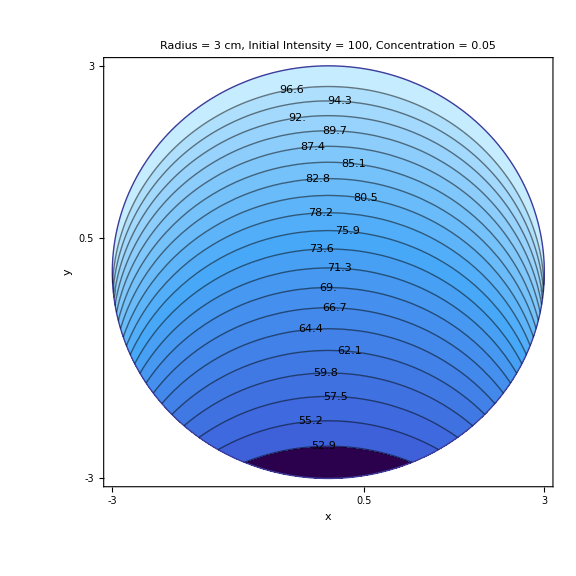
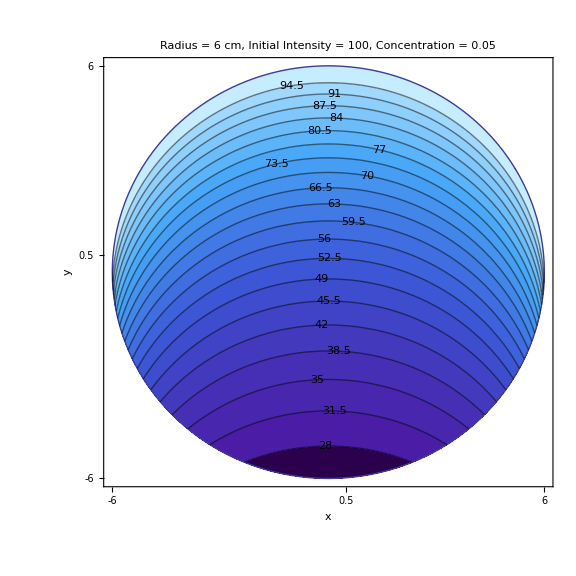
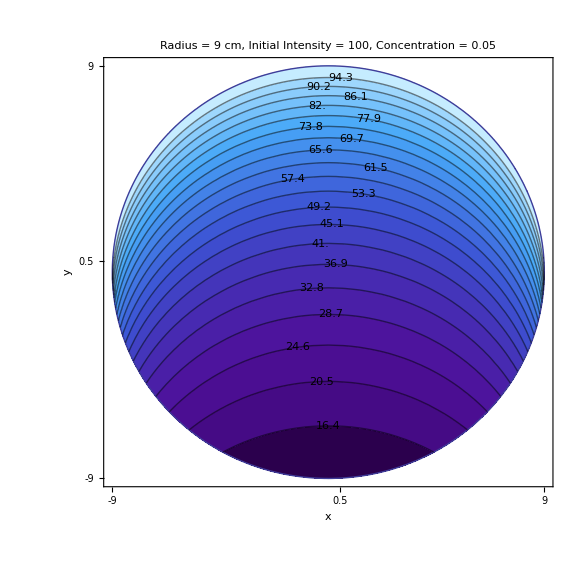

```mathematica
radiusVar = beerLambert[100,#, 0.05, "contour", {0,0}] & /@ {3, 6, 9}
```

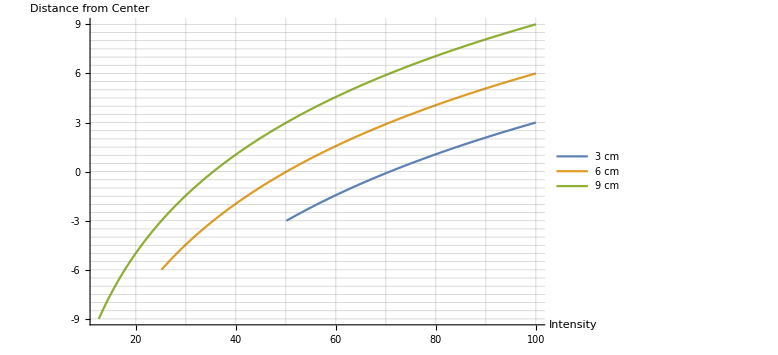

```mathematica
radiusVarLine = ListLinePlot[radiusVarNum, PlotRange-> {{100,0},{-9,9}}, GridLines -> {Range[0,100,10], Range[-9,9,0.5]}, AxesLabel->{"Intensity","Distance from Center"}, AxesOrigin->{0,0}, LabelStyle-> {Black,Bold, 11}, PlotLegends->{"3 cm", "6 cm", "9 cm"}, ImageSize->Large, Ticks-> {Transpose[{Range[0,100,10], Range[0,100,10]}], Transpose[{Range[-9,9,1], Range[-9,9,1]}]}]
```

### Fix the radius and the concentration and vary the intensity

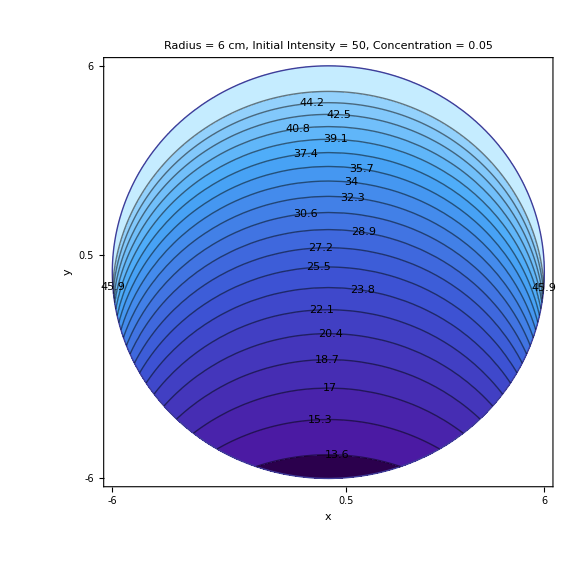
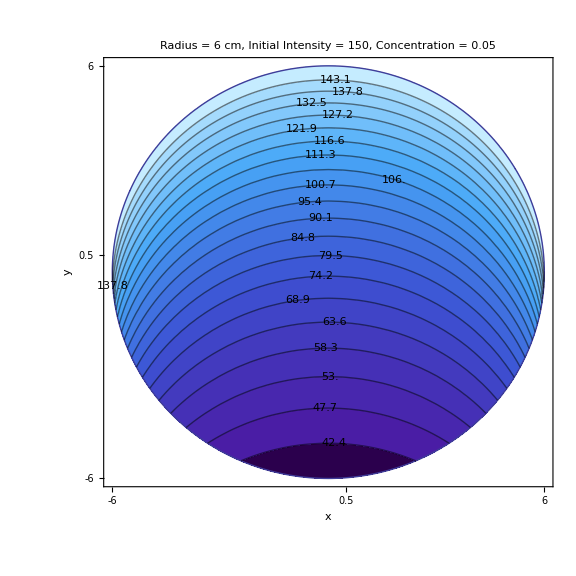
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
intensityVar = beerLambert[#, 6, 0.05, "contour", {0,0}] & /@ {50, 100, 150}
```

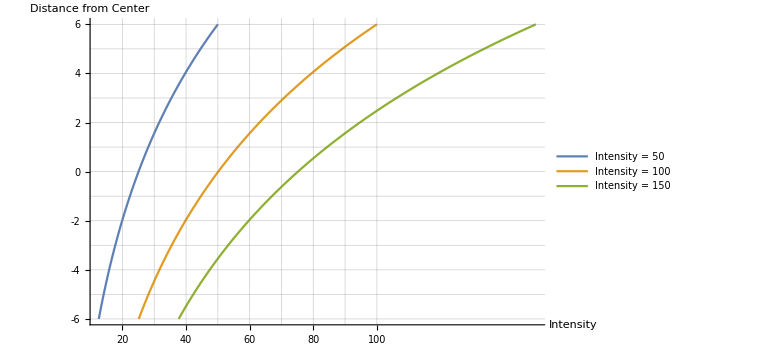

```mathematica
intensityVarLine = ListLinePlot[intensityVarNum, PlotRange-> {{100,0},{-6,6}}, GridLines -> {Range[0,100,10], Range[-6,6,1]}, AxesLabel->{"Intensity","Distance from Center"}, AxesOrigin->{0,0}, LabelStyle-> {Black,Bold, 11}, PlotLegends->{"Intensity = 50", "Intensity = 100", "Intensity = 150"}, ImageSize->Large, Ticks-> {Transpose[{Range[0,100,10], Range[0,100,10]}], Transpose[{Range[-6,6,1], Range[-6,6,1]}]}]
```

### Fix the radius and the intensity and vary the concentration

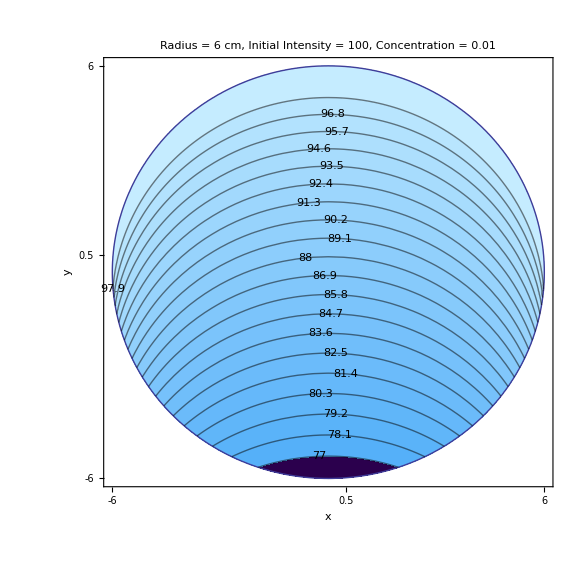
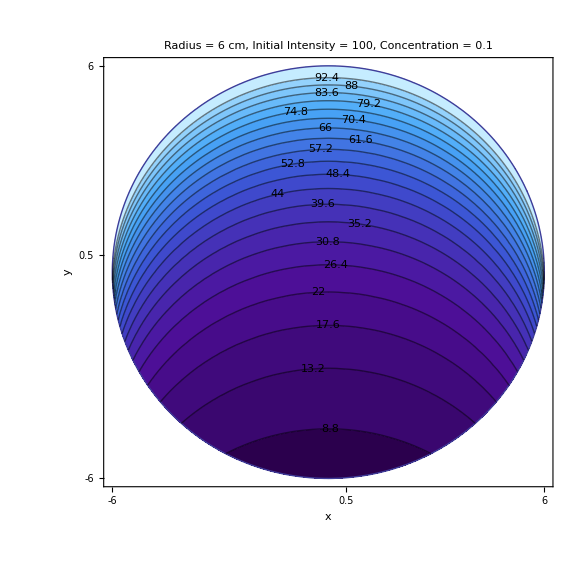
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
concentrationVar = beerLambert[100, 6, #, "contour", {0,0}] & /@ {0.01, 0.05, 0.1}
```

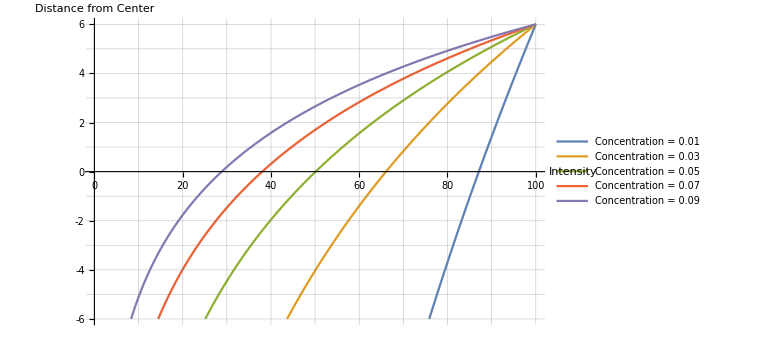

```mathematica
concVarLine = ListLinePlot[concVarNum, GridLines -> {Range[0,100,10], Range[-6,6,1]}, AxesLabel->{"Intensity","Distance from Center"}, AxesOrigin->{0,0}, LabelStyle-> {Black,Bold, 11}, PlotLegends->{"Concentration = 0.01", "Concentration = 0.03", "Concentration = 0.05", "Concentration = 0.07", "Concentration = 0.09"},ImageSize->Large, Ticks-> {Transpose[{Range[0,100,10], Range[0,100,10]}], Transpose[{Range[-6,6,1], Range[-6,6,1]}]}]
```